```mathematica
MatrixForm[Chop[Table[1/2∫_-1^1 LegendreP[i,w]LegendreP[j,w]ⅆw,{i,0,5},{j,0,5}]]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 0 | 0 | 0 | 0
0 | 0 | 1/5 | 0 | 0 | 0
0 | 0 | 0 | 1/7 | 0 | 0
0 | 0 | 0 | 0 | 1/9 | 0
0 | 0 | 0 | 0 | 0 | 1/11)

```mathematica
name="legen";
```

```mathematica
If[name=="legen",{cf[-1]:=0;cf[n_]:= (π(n+1))/(√(4(n+1)^2-1))},
{Print["ERROR"]; Quit[];}];
```

Orthogonal polynomials P_n(w)=P[n,w]   for the bandwidth  π:

```mathematica
P[0,w_]=1; 
P[1,w_]:=w/cf[0];
P[deg_,w_]:=P[deg,w]=w/cf[deg-1] P[deg-1,w]-cf[deg-2]/cf[deg-1] P[deg-2,w];
```

```mathematica
Expand[P[3,x]]
```

-(3 √7 x)/(2 π)+(5 √7 x^3)/(2 π^3)

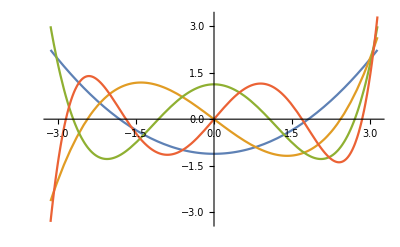

```mathematica
Plot[{P[2,x],P[3,x],P[4,x],P[5,x]},{x,-π,π}]
```

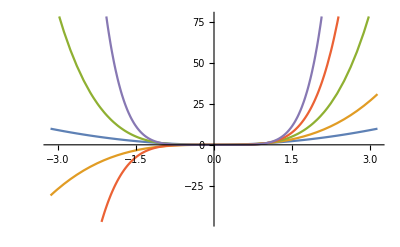

```mathematica
Plot[{x^2,x^3,x^4,x^5,x^6},{x,-π,π}]
```

```mathematica
MatrixForm[Chop[Table[1/(2 Pi)∫_-Pi^Pi P[i,w]P[j,w]ⅆw,{i,0,5},{j,0,5}]]]
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

Chromatic derivatives, for functions with one free parameter (variable) m with the bandwidth π:

K[f, n, m, t] = K^n[f(m,t)]

```mathematica
K[f_,0,m_,t_]:=f[m,t];
K[f_,1,m_,t_] := D[f[m,t], t]/cf[0];
K[f_,n_,m_,t_] :=K[f,n,m,t] =Expand[(1/cf[n-1] D[K[f,n-1,m,t], t]+cf[n-2]/cf[n-1] K[f,n-2,m,t])];
```

```mathematica
ew[w_,t_]:=ⅇ^(ⅈ w t);
```

```mathematica
P[3, n] // FullSimplify
```

(√7 n (5 n^2-3 π^2))/(2 π^3)

```mathematica
K[4x Cos[t],3,x,t] // FullSimplify
```

1/(cf[0] cf[1] cf[2])((4 x Sin[t])[x,t]+(cf[0]^2+cf[1]^2) ((-4 x Sin[t])[x,t]+(4 x Cos[t])^(0,1)[x,t])+3 ((-4 x Cos[t])^(0,1)[x,t]+(-4 x Sin[t])^(0,2)[x,t])+(4 x Cos[t])^(0,3)[x,t])

```mathematica
Function[{w,t},ⅇ^(ⅈ w t)]
```

Function[{w,t},ⅇ^(ⅈ w t)]

```mathematica
K[Function[{w,t},4Cos[t]+Exp[t]],2,w,t] // FullSimplify
```

(√5 (ⅇ^t (3+π^2)+4 (-3+π^2) Cos[t]))/(2 π^2)

```mathematica
ⅈ^2 P[2,w] ⅇ^(ⅈ w t) // FullSimplify
```

(√5 ⅇ^(ⅈ t w) (π^2-3 w^2))/(2 π^2)

```mathematica
FullSimplify[Table[K[ew,j,w,t]-ⅈ^j P[j,w] ⅇ^(ⅈ w t),{j,0,8}]]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
B[n_,t_]:=√(2n+1)SphericalBesselJ[n,π t];
```

```mathematica
g[w_,t_]:= 2 Sin[3t]+Cos[ 2t];

TK=N[FullSimplify[Table[K[g,j,w,t],{j,0,32}]]/.t-> 0];

TD=N[Table[D[g[w,t],{t,j}],{j,0,32}]/.t-> 0];
App[n_,t_]:=∑_(j=0)^n TK[[j+1]]B[j,t];
Taylor[n_,t_]:=∑_(j=0)^n TD[[j+1]] t^j/(j!);
```

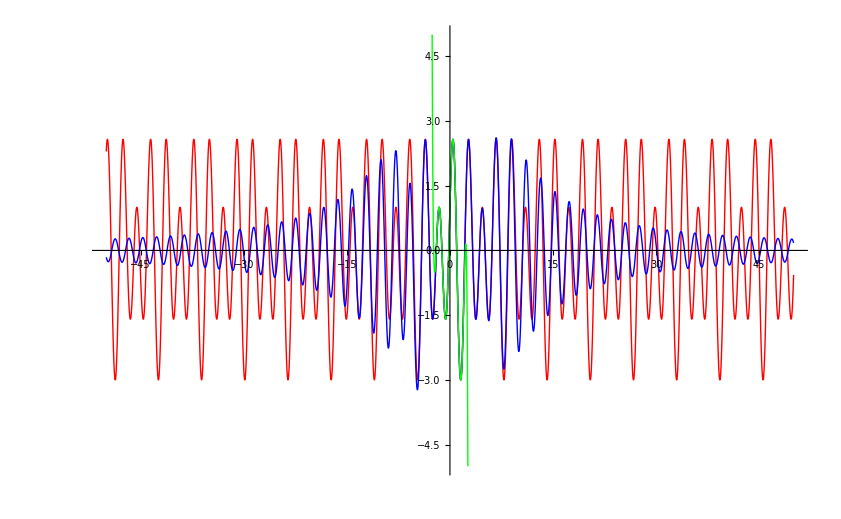

```mathematica
Plot[{g[0,t],App[15,t],Taylor[15,t]},{t,-50,50}, PlotStyle-> {Red,Blue,Green}, PlotRange-> {-5,5}]
```

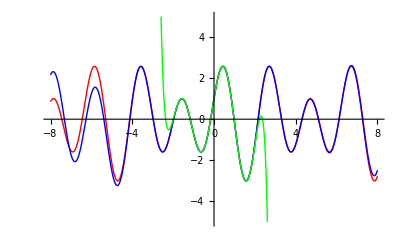

```mathematica
Plot[{g[0,t],App[15,t],Taylor[15,t]},{t,-8,8}, PlotStyle-> {Red,Blue,Green}, PlotRange-> {-5,5}]
```

```mathematica
FullSimplify[Table[K[B,j,0,t]-(-1)^j B[j,t],{j,0,8}],Assumptions-> t≠ 0]
```

{0,0,0,0,0,0,0,0,0}

Deriving recursion formula for K^n[B_m(t)]:

```mathematica
Table[FullSimplify[K[B,1,n,t]-(cf[n-1]/cf[0] B[n-1,t]-cf[n]/cf[0] B[n+1,t]),Assumptions-> t≠ 0],{n,0,8}]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
(*T=Flatten[Table[Chop[KC[B,m+1,n,t]-(cf[n-1]/cf[m] KC[B,m,n-1,t]-cf[n]/cf[m] KC[B,m,n+1,t]+cf[n-1]/cf[m] KC[B,m-1,n,t])],{n,0,10},{m,1,10}]];*)
```

```mathematica
(*Plot[Chop[T[[6]]],{t,-10,10}]*)
```

```mathematica
Flatten[Table[FullSimplify[Chop[K[B,m+1,n,t]-(1/cf[m] D[K[B,m,n,t], t]+cf[m-1]/cf[m] K[B,m-1,n,t])],Assumptions-> t≠ 0],{n,0,5},{m,1,5}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten[Table[FullSimplify[Chop[D[K[B,m,n,t], t]-(-cf[n] K[B,m,n+1,t]+cf[n-1]K[B,m,n-1,t])],Assumptions-> t≠ 0],{n,1,5},{m,1,5}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten[Table[FullSimplify[K[B,m+1,n,t]-(1/cf[m](-cf[n] K[B,m,n+1,t]+cf[n-1]K[B,m,n-1,t])+cf[m-1]/cf[m] K[B,m-1,n,t]),Assumptions-> t≠ 0],{n,1,5},{m,1,5}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Flatten[Table[FullSimplify[K[B,m+1,n,t]-(cf[n-1]/cf[m] K[B,m,n-1,t]+cf[m-1]/cf[m] K[B,m-1,n,t]-cf[n]/cf[m] K[B,m,n+1,t]),Assumptions-> t≠ 0],{n,1,5},{m,1,5}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

KC[B,m,0,t]=K^m[B_0(t)]=(-1)^m B_m(t);

KC[B,0,n,t]=B_n(t);

KC[B,1,n,t]=K^1[B_n(t)]=cf[n-1]/cf[0]B_(n-1)(t)-cf[n]/cf[0]B_(n+1)(t);    (redundant - see below)

KC[B,m+1,n,t]=K^(m+1)[B_n(t)]=cf[n-1]/cf[m]K^m[B_(n-1)(t)]+cf[m-1]/cf[m]K^(m-1)[B_n(t)]-cf[n]/cf[m]K^m[B_(n+1)(t)]; 
(implies the previous one (for m=0 ) as we set  cf[-1] = 0 )